```mathematica
l=0.030; (*ancho en metros*)
μ=4π*10^-7;
n=60;
r=0.1525; (*radio del solenoide en metros*)
```

```mathematica
solenoide[i_,k_]:=(μ n i)/(2 l)((k+l/2)/(√(r^2+(k+l/2)^2))-(k-l/2)/(√(r^2+(k-l/2)^2)))*10^3 (*Output en miliTesta, por eso el 10^3*)
```

```mathematica
espira[i_,r_,z_]:=(μ n i)/2(r^2/((√(r^2+(z)^2))^3))*10^3
```

```mathematica
datos=Flatten[
{{{"I","B error","B"},{0.1,-0.076,0.045},{0.22,-0.02,0.10099999999999999},{0.34,0.032,0.153},{0.51,0.099,0.22},{0.68,0.171,0.29200000000000004},{0.78,0.208,0.32899999999999996},{0.91,0.258,0.379},{1.02,0.301,0.422},{1.1,0.338,0.459},{1.21,0.379,0.5},{1.3,0.414,0.5349999999999999}},{{"I","B error","B"},{0.1,-0.178,0.036000000000000004},{0.2,-0.148,0.066},{0.3,-0.117,0.09699999999999999},{0.45,-0.074,0.14},{0.52,-0.057,0.157},{0.66,-0.02,0.194},{0.77,0.003,0.217},{0.82,0.014,0.228},{1.02,0.065,0.279}},{{"d","B error","B","I0",""},{20.,-0.018,0.10099999999999999,1.14,""},{18.,-0.012,0.107,"",""},{16.,0.036,0.155,"",""},{14.,0.076,0.195,"",""},{12.,0.117,0.236,"",""},{10.,0.164,0.28300000000000003,"",""},{8.,0.221,0.33999999999999997,"",""},{6.,0.279,0.398,"",""},{"","","","",""}}},1
];
```

```mathematica
datos//TableForm
```

I | B error | B |  | 
0.1 | -0.076 | 0.045 |  | 
0.22 | -0.02 | 0.101 |  | 
0.34 | 0.032 | 0.153 |  | 
0.51 | 0.099 | 0.22 |  | 
0.68 | 0.171 | 0.292 |  | 
0.78 | 0.208 | 0.329 |  | 
0.91 | 0.258 | 0.379 |  | 
1.02 | 0.301 | 0.422 |  | 
1.1 | 0.338 | 0.459 |  | 
1.21 | 0.379 | 0.5 |  | 
1.3 | 0.414 | 0.535 |  | 
I | B error | B |  | 
0.1 | -0.178 | 0.036 |  | 
0.2 | -0.148 | 0.066 |  | 
0.3 | -0.117 | 0.097 |  | 
0.45 | -0.074 | 0.14 |  | 
0.52 | -0.057 | 0.157 |  | 
0.66 | -0.02 | 0.194 |  | 
0.77 | 0.003 | 0.217 |  | 
0.82 | 0.014 | 0.228 |  | 
1.02 | 0.065 | 0.279 |  | 
d | B error | B | I0 | 
20. | -0.018 | 0.101 | 1.14 | 
18. | -0.012 | 0.107 |  | 
16. | 0.036 | 0.155 |  | 
14. | 0.076 | 0.195 |  | 
12. | 0.117 | 0.236 |  | 
10. | 0.164 | 0.283 |  | 
8. | 0.221 | 0.34 |  | 
6. | 0.279 | 0.398 |  | 
 |  |  |  |

```mathematica
i=datos[[2;;12,1]]; (*corriente*)
b=datos[[2;;12,3]]; (*campo medido*)
ip=datos[[14;;22,1]]; (*corriente perpendicular*)
bp=datos[[14;;22,3]]; (*campo perpendicular*)
z=datos[[24;;31,1]]*10^-2; (*distancia en metros*)
bd=datos[[24;;31,3]]; (*campo variando la distancia*)
bder=datos[[24;;31,2]]; (*ruido del campo, variando la distancia*)
id=datos[[24,4]]; (*corriente utilizaada*)
```

## Variacion de Distancia, solenoide

#### Teorico

```mathematica
datateorica=Table[{z[[n]],solenoide[id,z[[n]]]},{n,Length[z]}]
```

{{0.2,0.00105108},{0.18,0.00254717},{0.16,0.00464494},{0.14,0.00753569},{0.12,0.0114291},{0.1,0.016508},{0.08,0.0228386},{0.06,0.0302371}}

```mathematica
TableForm[datateorica]
```

0.2 | 0.00105108
0.18 | 0.00254717
0.16 | 0.00464494
0.14 | 0.00753569
0.12 | 0.0114291
0.1 | 0.016508
0.08 | 0.0228386
0.06 | 0.0302371

#### Experimental

```mathematica
bd=datos[[24;;31,3]];
dataexp=Table[{z[[n]],bd[[n]]},{n,Length[z]}]
```

{{0.2,0.101},{0.18,0.107},{0.16,0.155},{0.14,0.195},{0.12,0.236},{0.1,0.283},{0.08,0.34},{0.06,0.398}}

```mathematica
TableForm[dataexp]
```

0.2 | 0.101
0.18 | 0.107
0.16 | 0.155
0.14 | 0.195
0.12 | 0.236
0.1 | 0.283
0.08 | 0.34
0.06 | 0.398

```mathematica
bd
```

{0.101,0.107,0.155,0.195,0.236,0.283,0.34,0.398}

```mathematica
bdn=Sort[bd,Greater]
```

{0.398,0.34,0.283,0.236,0.195,0.155,0.107,0.101}

#### Haciendo un grafico y guardandolo

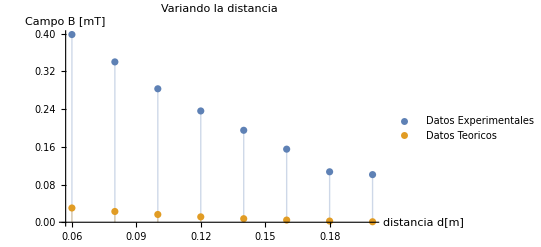

```mathematica
ListPlot[{dataexp,datateorica},PlotLabel->"Variando la distancia",Filling->Axis,PlotLegends->{"Datos Experimentales","Datos Teoricos"},AxesLabel->{"distancia d[m]","Campo B [mT]"}]
```

```mathematica
Export["d,b.jpg",%]
```

d,b.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["d,b.jpg"]]]
```

#### Fitting

```mathematica
FindFit[bdn,(μ n *1.14)/(2 l)((k+l/2)/(√(r^2+(k+l/2)^2))-(k-l/2)/(√(r^2+(k-l/2)^2)))*10^3,{n,k},]
```

FindFit[{0.398,0.34,0.283,0.236,0.195,0.155,0.107,0.101},1.65296 (-(-0.013+k)/(√(0.0232563+(-0.013+k)^2))+(0.013+k)/(√(0.0232563+(0.013+k)^2))),{60,k},Null]

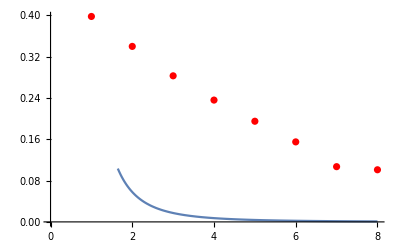

```mathematica
Show[ListPlot[bdn,PlotStyle->Red],Plot[((μ n y) ((k+l/2)/(√(r^2+(k+l/2)^2))-(k-l/2)/(√(r^2+(k-l/2)^2))) 10^3)/(2 l)/.{y->532.424},{k,1,8}]]
```

## Variando la corriente, paralela al norte

### Teorico

```mathematica
datateoricapl=Table[{i[[n]],solenoide[i[[n]],l,r,0]},{n,Length[i]}]
```

{{0.1,0.000410523},{0.22,0.0018063},{0.34,0.00418734},{0.51,0.00837467},{0.68,0.0139578},{0.78,0.0192125},{0.91,0.0261503},{1.02,0.0334987},{1.1,0.0406418},{1.21,0.0496733},{1.3,0.0587048}}

```mathematica
TableForm[datateoricapl]
```

0.1 | 0.000410523
0.22 | 0.0018063
0.34 | 0.00418734
0.51 | 0.00837467
0.68 | 0.0139578
0.78 | 0.0192125
0.91 | 0.0261503
1.02 | 0.0334987
1.1 | 0.0406418
1.21 | 0.0496733
1.3 | 0.0587048

### Experimental

```mathematica
dataexppl=Table[{i[[n]],b[[n]]},{n,Length[b]}]
```

{{0.1,0.045},{0.22,0.101},{0.34,0.153},{0.51,0.22},{0.68,0.292},{0.78,0.329},{0.91,0.379},{1.02,0.422},{1.1,0.459},{1.21,0.5},{1.3,0.535}}

### Comparando resultados

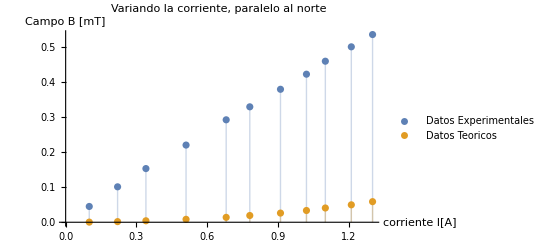

```mathematica
ListPlot[{dataexppl,datateoricapl},PlotLabel->"Variando la corriente, paralelo al norte",Filling->Axis,PlotLegends->{"Datos Experimentales","Datos Teoricos"},AxesLabel->{"corriente I[A]","Campo B [mT]"}]
```

```mathematica
Export["i,pp.jpg",%]
```

i,pp.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["i,p.jpg"]]]
```

### Encontrando un FIT a los datos

```mathematica
FindFit[dataexppl,(μ n y)/(2 l)((k+l/2)/(√(r^2+(k+l/2)^2))-(k-l/2)/(√(r^2+(k-l/2)^2)))*10^3,{k},y]
```

{k→7.36584×10^-10}

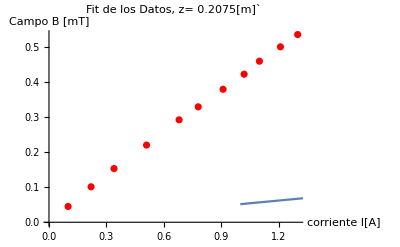

```mathematica
Show[ListPlot[dataexppl,PlotStyle->Red],Plot[((μ n y) ((k+l/2)/(√(r^2+(k+l/2)^2))-(k-l/2)/(√(r^2+(k-l/2)^2))) 10^3)/(2 l)/.{k->0.207454085371166},{y,1,11}],PlotLabel->"Fit de los Datos, z= 0.2075[m]`",AxesLabel->{"corriente I[A]","Campo B [mT]"}]
```

```mathematica
b
```

{0.045,0.101,0.153,0.22,0.292,0.329,0.379,0.422,0.459,0.5,0.535}

## Variando la corriente, perpendicular al norte

### Teorico

```mathematica
datateoricapp=Table[{ip[[n]],solenoide[i[[n]],l,r,0]},{n,Length[ip]}]
```

{{0.1,0.000410523},{0.2,0.0018063},{0.3,0.00418734},{0.45,0.00837467},{0.52,0.0139578},{0.66,0.0192125},{0.77,0.0261503},{0.82,0.0334987},{1.02,0.0406418}}

```mathematica
TableForm[datateoricapp]
```

0.1 | 0.000410523
0.2 | 0.0018063
0.3 | 0.00418734
0.45 | 0.00837467
0.52 | 0.0139578
0.66 | 0.0192125
0.77 | 0.0261503
0.82 | 0.0334987
1.02 | 0.0406418

```mathematica
dataexppp=Table[{ip[[n]],bp[[n]]},{n,Length[bp]}]
```

{{0.1,0.036},{0.2,0.066},{0.3,0.097},{0.45,0.14},{0.52,0.157},{0.66,0.194},{0.77,0.217},{0.82,0.228},{1.02,0.279}}

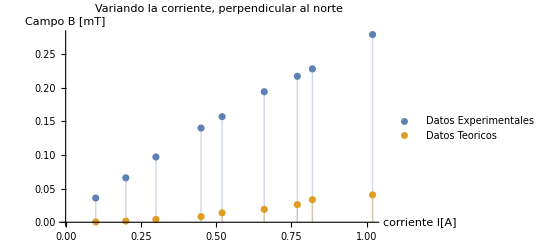

```mathematica
ListPlot[{dataexppp,datateoricapp},PlotLabel->"Variando la corriente, perpendicular al norte",Filling->Axis,PlotLegends->{"Datos Experimentales","Datos Teoricos"},AxesLabel->{"corriente I[A]","Campo B [mT]"}]
```